## The staggering effect in ^163 Lu TSD1-2

```mathematica
spin1=Table[25/2+2i,{i,0,16}];
spin2=Table[27/2+2i,{i,0,16}];
tsd1={2.5145,2.9008,3.3511,3.8664,4.445,5.084,5.781,6.5336,7.3391,8.1969,9.1066,10.0692,11.0857,12.1568,13.283,14.4623,15.689};
tsd2={3.0793,3.4866,3.9583,4.4926,5.0883,5.7429,6.4542,7.2204,8.0403,8.9132,9.8397,10.8199,11.8546,12.9435,14.0865,15.284,16.531};
```

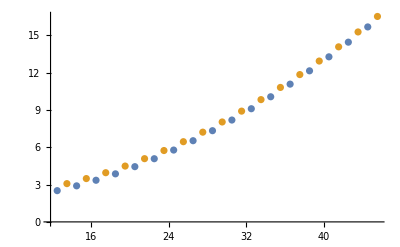

```mathematica
ListPlot[{Table[{spin1[[i]],tsd1[[i]]},{i,1,Length[spin1]}],Table[{spin2[[i]],tsd2[[i]]},{i,1,Length[spin2]}]}]
```